```mathematica
x - миллиметры;
t - микросекунды;
T - градусы;
```

```mathematica
cv=24.27/(9.53 10^3);
λ=162.8 10^-9;
```

```mathematica
s=NDSolve[{cv D[T[t,x],t]==D[λ D[T[t,x],x],x],(λ D[T[t,x],x]/.x->0)==(1750-273)(1/(π 5^2))Tanh[10t]((Tanh[10(t-150)]-1)/(2 2.7190819255176567*^7 0.4645707209205219)),(D[T[t,x],x]/.x->2.1)==0,T[0,x]==0},T,{t,0,100000},{x,0,2.1},AccuracyGoal->20,PrecisionGoal->10,Method->{"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}}]
```

General::munfl: Sech[-1500.] is too small to represent as a normalized machine number; precision may be lost.

{{T→InterpolatingFunction[{{0., 100000.}, {0., 2.1}}, <>]}}

```mathematica
Tn[t_,x_]:=Evaluate[T[t,x]/.s][[1]]
```

```mathematica
Tn[150,0]
```

1.

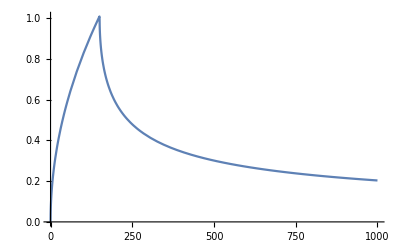

```mathematica
Plot[Tn[t,0],{t,0,1000},PlotRange->All]
```

```mathematica
Tn[t_,x_,r_]:=(910-273) 2^(-(r/(5/2))^2)Evaluate[T[t,x]/.s][[1]]
```

```mathematica
Plot3D[Tn[t,x,0],{t,0,10000},{x,0,2.1},PlotRange->All]
```

-Graphics3D-

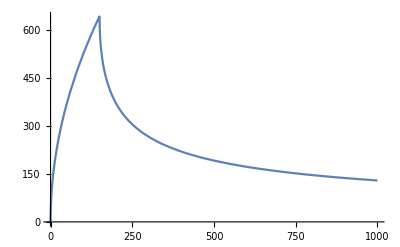

```mathematica
Plot[Tn[t,0,0],{t,0,1000},PlotRange->All]
```

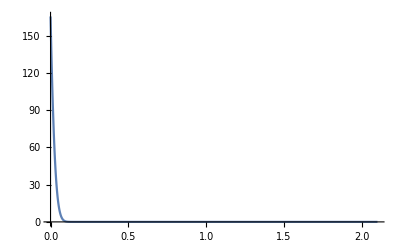

```mathematica
Plot[Tn[10,x,0],{x,0,2.1},PlotRange->All]
```